```mathematica
Clear[ψ1slit,ρ1slit,x,t,k,k,a,s,u,v];
```

```mathematica
Clear[w,ρ2slits,solution,a,n0,D1,L,k,s,x,t,slope,slope0,S1,G1,K1,K2,c1,b1];
```

```mathematica
Clear[a,x,s,t,b,c1,PS,S1,Ref1,Imf1,X0,C1,c1,S1];
```

```mathematica
ψ1slit[x_,t_,a_,k_]:=(ⅇ^(-(ⅈ k^2 t+2 ⅈ √2 a k (-x)+x^2)/(4 a^2+2 ⅈ t)) (2/π)^(1/4))/(√a √(2+(ⅈ t)/a^2));
ρ1slit[x_,t_,a_,k_]:=(a ⅇ^(-Re[(k t+√2 a (-x))^2/(4 a^4+t^2)]) √(2/π))/(√(4 a^4+t^2));
```

```mathematica
Simplify[ⅈ/2 D[ψ1slit[x,t,a,k], {x,2}]-D[ψ1slit[x,t,a,k], {t,1}]]
```

0

```mathematica
a=1.0;  s=1.0;b=.1;  k=0.0;  (* ENTER BELOW, TOO *)
```

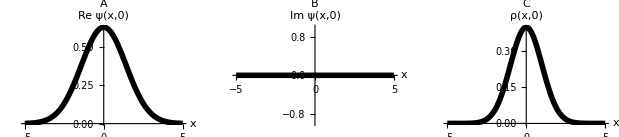

```mathematica
WA=Plot[Re[ψ1slit[x,0,a,k]],{x,-5,5},AspectRatio->.7,PlotRange->All,AxesLabel->{"x","Re ψ(x,0)"},PlotStyle->{Black,Thickness[.01]},PlotLabel->"A"];
WB=Plot[Im[ψ1slit[x,0,a,k]],{x,-5,5},AspectRatio->.7,PlotRange->All,AxesLabel->{"x","Im ψ(x,0)"},PlotStyle->{Black,Thickness[.01]},PlotLabel->"B"];
WC=Plot[ρ1slit[x,0,a,k],{x,-5,5},AspectRatio->.7,PlotRange->All,AxesLabel->{"x","ρ(x,0)"},PlotStyle->{Black,Thickness[.01]},PlotLabel->"C"];
GraphicsRow[{WA,WB,WC},Frame->True]
```

```mathematica
∫_-10^10 ρ1slit[x,0,a,k]ⅆx//N
```

1.

```mathematica
Clear[a,b,s,k]
```

```mathematica
ComplexExpand[ψ1slit[x,0,a,k]]
```

((a^2)^(3/4) ⅇ^(-x^2/(4 a^2)) Cos[(k x)/(√2 a)] Cos[Arg[a]/2])/(a^2 (2 π)^(1/4))+((a^2)^(3/4) ⅇ^(-x^2/(4 a^2)) Sin[(k x)/(√2 a)] Sin[Arg[a]/2])/(a^2 (2 π)^(1/4))+ⅈ (((a^2)^(3/4) ⅇ^(-x^2/(4 a^2)) Cos[Arg[a]/2] Sin[(k x)/(√2 a)])/(a^2 (2 π)^(1/4))-((a^2)^(3/4) ⅇ^(-x^2/(4 a^2)) Cos[(k x)/(√2 a)] Sin[Arg[a]/2])/(a^2 (2 π)^(1/4)))

```mathematica
Ref[x_]:=((a^2)^(3/4) ⅇ^(-x^2/(4 a^2)) Cos[(k x)/(√2 a)] Cos[Arg[a]/2])/(a^2 (2 π)^(1/4))+((a^2)^(3/4) ⅇ^(-x^2/(4 a^2)) Sin[(k x)/(√2 a)] Sin[Arg[a]/2])/(a^2 (2 π)^(1/4));
Imf[x_]:=((a^2)^(3/4) ⅇ^(-x^2/(4 a^2)) Cos[Arg[a]/2] Sin[(k x)/(√2 a)])/(a^2 (2 π)^(1/4))-((a^2)^(3/4) ⅇ^(-x^2/(4 a^2)) Cos[(k x)/(√2 a)] Sin[Arg[a]/2])/(a^2 (2 π)^(1/4));
```

```mathematica
Simplify[Ref[x]]
```

((a^2)^(3/4) ⅇ^(-x^2/(4 a^2)) Cos[(k x)/(√2 a)-Arg[a]/2])/(a^2 (2 π)^(1/4))

```mathematica
Simplify[Imf[x]]
```

((a^2)^(3/4) ⅇ^(-x^2/(4 a^2)) Sin[(k x)/(√2 a)-Arg[a]/2])/(a^2 (2 π)^(1/4))

```mathematica
Simplify[∫_(s-b)^(s+b) Ref[x]^2 ⅆx]
```

-1/(8 a^2 Conjugate[a])√(a^2) ⅇ^(-k^2) (ⅈ a Abs[a] (Erfi[k+(ⅈ (b-s))/(√2 a)]-Erfi[k-(ⅈ (b+s))/(√2 a)])+Conjugate[a] (2 a ⅇ^(k^2) (Erf[(-b+s)/(√2 a)]-Erf[(b+s)/(√2 a)])-ⅈ Abs[a] (Erfi[k+(ⅈ (-b+s))/(√2 a)]-Erfi[k+(ⅈ (b+s))/(√2 a)])))

```mathematica
Simplify[∫_(s-b)^(s+b) Imf[x]^2 ⅆx]
```

1/(8 a^2 Conjugate[a])√(a^2) ⅇ^(-k^2) (ⅈ a Abs[a] (Erfi[k+(ⅈ (b-s))/(√2 a)]-Erfi[k-(ⅈ (b+s))/(√2 a)])+Conjugate[a] (-2 a ⅇ^(k^2) (Erf[(-b+s)/(√2 a)]-Erf[(b+s)/(√2 a)])-ⅈ Abs[a] (Erfi[k+(ⅈ (-b+s))/(√2 a)]-Erfi[k+(ⅈ (b+s))/(√2 a)])))

```mathematica
c1[a_,b_,s_,k_]:=1/√(∫_(-s-b)^(-s+b) Ref[x]^2 ⅆx+∫_(-s-b)^(-s+b) Imf[x]^2 ⅆx+∫_(s-b)^(s+b) Ref[x]^2 ⅆx+∫_(s-b)^(s+b) Imf[x]^2 ⅆx);
```

```mathematica
a=1.0;  s=1.0;b=.1;  k=0.0;
```

```mathematica
c1[a,b,s,k]
```

3.21432

```mathematica
C1=Re[c1[a,b,s,k]]
```

3.21432

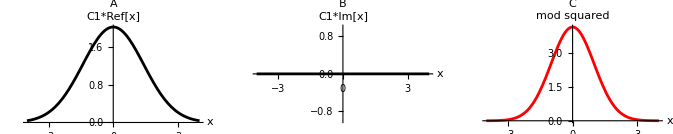

```mathematica
DWWWA=Plot[C1*Ref[x],{x,-4,4},AspectRatio->.3,PlotRange->All,AxesLabel->{"x","C1*Ref[x]"},PlotStyle->{Black,Thickness[.005]},PlotLabel->"A"];
DWWWB=Plot[C1*Imf[x],{x,-4,4},AspectRatio->.3,PlotRange->All,AxesLabel->{"x","C1*Im[x]"},PlotStyle->{Black,Thickness[.005]},PlotLabel->"B"];
DWWWC=Plot[(C1*Ref[x])^2+(C1*Imf[x])^2,{x,-4,4},AspectRatio->.7,PlotRange->All,AxesLabel->{"x","mod squared"},PlotStyle->{Red,Thickness[.005]},PlotLabel->"C"];
GraphicsRow[{DWWWA,DWWWB,DWWWC}]
```

```mathematica
Ref1[x_]:=0.0/;x<-s-b;
Ref1[x_]:=C1*Ref[x]/;-s-b≤x≤-s+b;
Ref1[x_]:=0.0/;-s+b<x<s-b;
Ref1[x_]:=C1*Ref[x]/;s-b<=x≤s+b;
Ref1[x_]:=0.0/;s+b<x;
```

```mathematica
Imf1[x_]:=0.0/;x<-s-b;
Imf1[x_]:=C1*Imf[x]/;-s-b≤x≤-s+b;
Imf1[x_]:=0.0/;-s+b<x<s-b;
Imf1[x_]:=C1*Imf[x]/;s-b<=x≤s+b;
Imf1[x_]:=0.0/;s+b<x;
```

```mathematica
∫_-4.0^4.0 Ref1[x]^2 ⅆx//N
```

1.00457

```mathematica
∫_-4.0^4.0 Imf1[x]^2 ⅆx//N
```

0.

```mathematica
(∫_-4.0^4.0 Ref1[x]^2 ⅆx+∫_-4.0^4.0 Imf1[x]^2 ⅆx)//N
```

1.00457

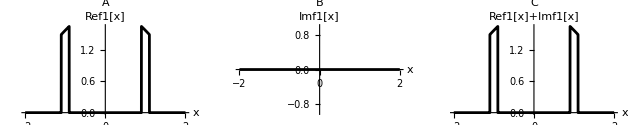

```mathematica
DWWA=Plot[Ref1[x],{x,-2,2},AspectRatio->.4,PlotRange->All,AxesLabel->{"x","Ref1[x]"},PlotStyle->{Black,Thickness[.005]},PlotLabel->"A"];
DWWB=Plot[Imf1[x],{x,-2,2},AspectRatio->.4,PlotRange->All,AxesLabel->{"x","Imf1[x]"},PlotStyle->{Black,Thickness[.005]},PlotLabel->"B"];
DWWC=Plot[Ref1[x]+Imf1[x],{x,-2,2},AspectRatio->.4,PlotRange->All,AxesLabel->{"x","Ref1[x]+Imf1[x]"},PlotStyle->{Black,Thickness[.005]},PlotLabel->"C"];
GraphicsRow[{DWWA,DWWB,DWWC}]
```

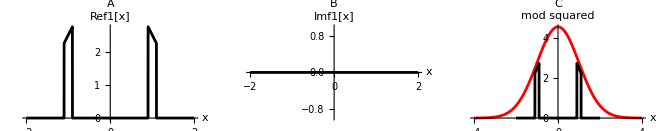

```mathematica
WA=Plot[Ref1[x]^2,{x,-2,2},AspectRatio->.4,PlotRange->All,AxesLabel->{"x","Ref1[x]"},PlotStyle->{Black,Thickness[.005]},PlotLabel->"A"];
WB=Plot[Imf1[x]^2,{x,-2,2},AspectRatio->.4,PlotRange->All,AxesLabel->{"x","Imf1[x]"},PlotStyle->{Black,Thickness[.005]},PlotLabel->"B"];
WC=Plot[Ref1[x]^2+Imf1[x]^2,{x,-2,2},AspectRatio->.4,PlotRange->All,AxesLabel->{"x","Ref1[x]^2+Imf1[x]^2"},PlotStyle->{Black,Thickness[.005]},PlotLabel->"C"];
GraphicsRow[{WA,WB,Show[{WWWC,WC}]}]
```

```mathematica
S1[x_,t_]:=1/(2π t)((∫_(-s-b)^(-s+b) (Cos[(x-y)^2/(2 t)]Ref1[y]-Sin[(x-y)^2/(2 t)]Imf1[y])ⅆy+∫_(s-b)^(s+b) (Cos[(x-y)^2/(2 t)]Ref1[y]-Sin[(x-y)^2/(2 t)]Imf1[y])ⅆy)^2
+(∫_(-s-b)^(-s+b) (Sin[(x-y)^2/(2 t)]Ref1[y]+Cos[(x-y)^2/(2 t)]Imf1[y])ⅆy+∫_(s-b)^(s+b) (Sin[(x-y)^2/(2 t)]Ref1[y]+Cos[(x-y)^2/(2 t)]Imf1[y])ⅆy)^2)//N
```

```mathematica
t1=1.0s^2/Pi
```

0.31831

0.31831

0.31831

```mathematica
b Pi
```

0.314159

0.314159

0.314159

```mathematica
Clear[TableD2];  imesh=2.5;  
xx[i_]:=i*imesh;  
TableD2=Table[{xx[i],S1[xx[i],100 t1]},{i,-400,400,imesh}];
```

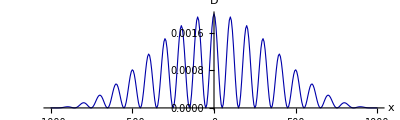

```mathematica
DD2=ListPlot[TableD2,AspectRatio->.3,PlotRange->All,AxesOrigin->{0,0},Joined->True,AxesStyle->Directive[Black,12],PlotStyle->{Thickness[.002],Darker[Blue]},AxesLabel->{"x",""},PlotLabel->"D"]
```

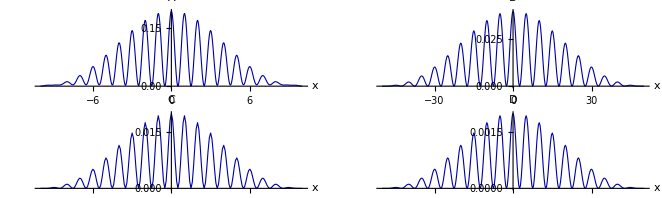

```mathematica
GraphicsGrid[{{AA2,BB2},{CC2,DD2}},AspectRatio->.5]
```